```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
FileExport[data_, filename_?StringQ] :=
With[
{folder=FileNameJoin[{NotebookDirectory[], "pic"}]},
If[FileType[folder]== None,CreateDirectory[folder]];
Export[FileNameJoin[{folder,StringJoin[filename, ".pdf"]}] , data, "PDF"];
];
```

```mathematica
(*
	I – Железо
II - Кадмий
*)
```

## Податливость S и упругость C. Матрицы коэффициентов

```mathematica
Subscript[C, I,11] = 234*10^9;
 Subscript[C, I, 12] =135*10^9; 
Subscript[C, I, 44]= 114*10^9;
```

```mathematica
Subscript[C, I]= ({{Subscript[C, I, 11], Subscript[C, I, 12], Subscript[C, I, 12], 0, 0, 0}, {Subscript[C, I, 12], Subscript[C, I, 11], Subscript[C, I, 12], 0, 0, 0}, {Subscript[C, I, 12], Subscript[C, I, 12], Subscript[C, I, 11], 0, 0, 0}, {0, 0, 0, Subscript[C, I, 44], 0, 0}, {0, 0, 0, 0, Subscript[C, I, 44], 0}, {0, 0, 0, 0, 0, Subscript[C, I, 44]}}); 10^-9 Subscript[C, I] // MatrixForm
```

(234 | 135 | 135 | 0 | 0 | 0
135 | 234 | 135 | 0 | 0 | 0
135 | 135 | 234 | 0 | 0 | 0
0 | 0 | 0 | 114 | 0 | 0
0 | 0 | 0 | 0 | 114 | 0
0 | 0 | 0 | 0 | 0 | 114)

```mathematica
Subscript[C, k] = (Subscript[C, I, 11]-Subscript[C, I, 12])*(Subscript[C, I, 11]+2 Subscript[C, I, 12]);
```

```mathematica
Subscript[S, I, 11]= N[(Subscript[C, I, 11]+ Subscript[C, I, 12])/Subscript[C, k]];
Subscript[S, I, 12]= N[(-Subscript[C, I, 12])/Subscript[C, k]];
Subscript[S, I, 44] = N[1/Subscript[C, I, 44]];
```

```mathematica
Subscript[S, I]= ({{Subscript[S, I, 11], Subscript[S, I, 12], Subscript[S, I, 12], 0, 0, 0}, {Subscript[S, I, 12], Subscript[S, I, 11], Subscript[S, I, 12], 0, 0, 0}, {Subscript[S, I, 12], Subscript[S, I, 12], Subscript[S, I, 11], 0, 0, 0}, {0, 0, 0, Subscript[S, I, 44], 0, 0}, {0, 0, 0, 0, Subscript[S, I, 44], 0}, {0, 0, 0, 0, 0, Subscript[S, I, 44]}}); 10^12*Subscript[S, I] // MatrixForm
```

(7.39538 | -2.70563 | -2.70563 | 0 | 0 | 0
-2.70563 | 7.39538 | -2.70563 | 0 | 0 | 0
-2.70563 | -2.70563 | 7.39538 | 0 | 0 | 0
0 | 0 | 0 | 8.77193 | 0 | 0
0 | 0 | 0 | 0 | 8.77193 | 0
0 | 0 | 0 | 0 | 0 | 8.77193)

```mathematica
(* Точность обращения матрицы упругих коэффицинетов *)
```

```mathematica
Norm[Inverse[N[Subscript[C, I]]]-Subscript[S, I]]
```

1.92018×10^-27

```mathematica
Subscript[S, II, 11]= 12.4 * 10^-12;
Subscript[S, II, 12]= -0.76 * 10^-12;
Subscript[S, II, 13]= -9.97 * 10^-12;
Subscript[S, II, 33]= 37.5 * 10^-12;
Subscript[S, II, 44]= 63.7 * 10^-12;
Subscript[S, II, 66]= 2*(Subscript[S, II, 11]- Subscript[S, II, 12]);
```

```mathematica
Subscript[S, II]= ({{Subscript[S, II, 11], Subscript[S, II, 12], Subscript[S, II, 13], 0, 0, 0}, {Subscript[S, II, 12], Subscript[S, II, 11], Subscript[S, II, 13], 0, 0, 0}, {Subscript[S, II, 13], Subscript[S, II, 13], Subscript[S, II, 33], 0, 0, 0}, {0, 0, 0, Subscript[S, II, 44], 0, 0}, {0, 0, 0, 0, Subscript[S, II, 44], 0}, {0, 0, 0, 0, 0, Subscript[S, II, 66]}}) ;10^12 Subscript[S, II] // MatrixForm
```

(12.4 | -0.76 | -9.97 | 0 | 0 | 0
-0.76 | 12.4 | -9.97 | 0 | 0 | 0
-9.97 | -9.97 | 37.5 | 0 | 0 | 0
0 | 0 | 0 | 63.7 | 0 | 0
0 | 0 | 0 | 0 | 63.7 | 0
0 | 0 | 0 | 0 | 0 | 26.32)

```mathematica
Subscript[S, r]= (Subscript[S, II, 11]+Subscript[S, II, 12])Subscript[S, II, 33]- 2(Subscript[S, II, 13])^2;
```

```mathematica
Subscript[C, II, 11]=N[ (Subscript[S, II, 33]/(2 Subscript[S, r])+0.5/(Subscript[S, II, 11]-Subscript[S, II, 12]))];
Subscript[C, II, 12]= N[ (Subscript[S, II, 33]/(2 Subscript[S, r])-0.5/(Subscript[S, II, 11]-Subscript[S, II, 12]))];
Subscript[C, II, 13]= N[ ((-Subscript[S, II, 13])/Subscript[S, r])];
Subscript[C, II, 33]=N[ ((Subscript[S, II, 11]+Subscript[S, II, 12])/Subscript[S, r])];
Subscript[C, II, 44]= N[ (1/Subscript[S, II, 44])];
Subscript[C, II, 66]= N[ (1/Subscript[S, II, 66])];
```

```mathematica
Subscript[C, II]= ({{Subscript[C, II, 11], Subscript[C, II, 12], Subscript[C, II, 13], 0, 0, 0}, {Subscript[C, II, 12], Subscript[C, II, 11], Subscript[C, II, 13], 0, 0, 0}, {Subscript[C, II, 13], Subscript[C, II, 13], Subscript[C, II, 33], 0, 0, 0}, {0, 0, 0, Subscript[C, II, 44], 0, 0}, {0, 0, 0, 0, Subscript[C, II, 44], 0}, {0, 0, 0, 0, 0, Subscript[C, II, 66]}}) ; 10^-9 Subscript[C, II] // MatrixForm
```

(116.875 | 40.8876 | 41.9439 | 0 | 0 | 0
40.8876 | 116.875 | 41.9439 | 0 | 0 | 0
41.9439 | 41.9439 | 48.9697 | 0 | 0 | 0
0 | 0 | 0 | 15.6986 | 0 | 0
0 | 0 | 0 | 0 | 15.6986 | 0
0 | 0 | 0 | 0 | 0 | 37.9939)

```mathematica
Norm[Inverse[N[Subscript[S, II]]]-Subscript[C, II]]
```

0.0000152588

## Зависимость линейной податливости от направления единичного вектора

```mathematica
Subscript[S, I, n][n1_,n2_, n3_] := 10^12(Subscript[S, I,11]- Subscript[S, I,44]((2( Subscript[S, I,11]- Subscript[S, I,12]))/Subscript[S, I,44]-1)(n1^2 n2^2+n1^2 n3^3+n2^2 n3^2))
```

```mathematica
Subscript[S, II, n][n1_,n2_, n3_] := 10^12(Subscript[S, II,11]- Subscript[S, II,44]((2( Subscript[S, II,11]- Subscript[S, II,12]))/Subscript[S, II,44]-1)(n1^2 n2^2+n1^2 n3^3+n2^2 n3^2))
```

```mathematica
Subscript[f, II][n_]:= 10^12(Subscript[S, II,11] (1-n^2)+ Subscript[S, II,13] n^4+(2 Subscript[S, II,13]+Subscript[S, II,44])n^2(1-n^2))
```

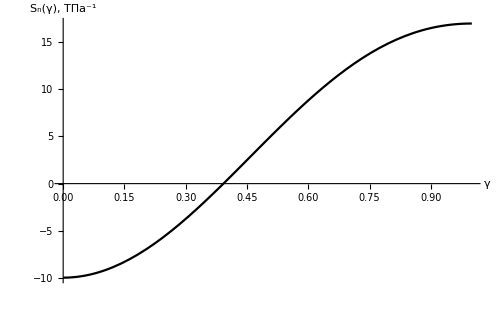

```mathematica
plot1 = Plot[Subscript[f, II][Cos[γ]], {γ, 0 , 1},
PlotStyle->{Black, Bold},
AxesLabel->{Style["γ", Large,Black],Style["S_n(γ), (T:041f:0430)^-1",Large,Black]},AxesStyle->Thick, BaseStyle->Directive[FontSize->17,FontWeight->Plain],ImageSize->500]
FileExport[plot1, "II_1"];
```

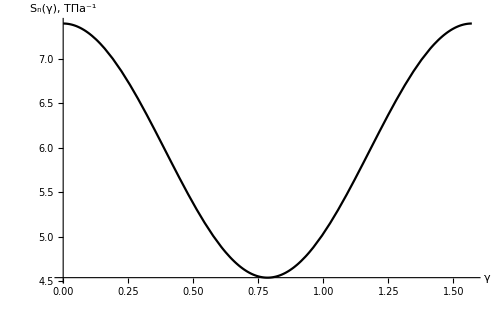

```mathematica
plot2 = Plot[Subscript[S, I, n][Cos[γ],Sin[γ],0], {γ, 0 , π/2},
PlotStyle->{Black, Bold},
AxesLabel->{Style["γ",Large,Black],Style["S_n(γ), (T:041f:0430)^-1",Large,Black]},AxesStyle->Thick, BaseStyle->Directive[FontSize->17,FontWeight->Plain],ImageSize->500]
FileExport[plot2, "I_1"];
```

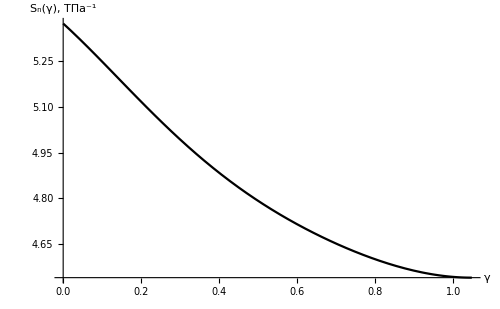

```mathematica
plot3 = Plot[Subscript[S, I, n][1/(√2)Cos[γ]-1/(√6)Sin[γ],√(2/3)Sin[γ],1/(√2)Cos[γ]+1/(√6)Sin[γ]], {γ, 0 , π/3},
PlotStyle->{Black, Bold},
AxesLabel->{Style["γ",Large,Black],Style["S_n(γ), (T:041f:0430)^-1",Large,Black]},AxesStyle->Thick, BaseStyle->Directive[FontSize->17,FontWeight->Plain],ImageSize->500]
FileExport[plot3, "I_2"];
```

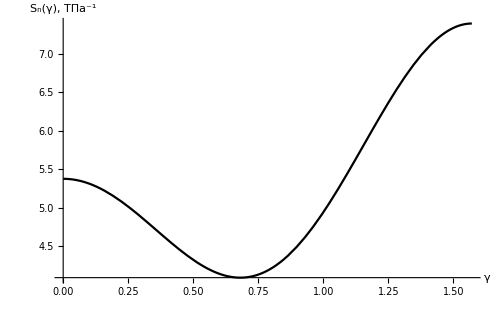

```mathematica
plot4 = Plot[Subscript[S, I, n][1/(√2)Cos[γ],Sin[γ],1/(√2)Cos[γ]], {γ, 0 , π/2},
PlotStyle->{Black, Bold},
AxesLabel->{Style["γ",Large,Black],Style["S_n(γ), (T:041f:0430)^-1",Large,Black]},AxesStyle->Thick, BaseStyle->Directive[FontSize->17,FontWeight->Plain],ImageSize->500]
FileExport[plot4, "I_3"];
```

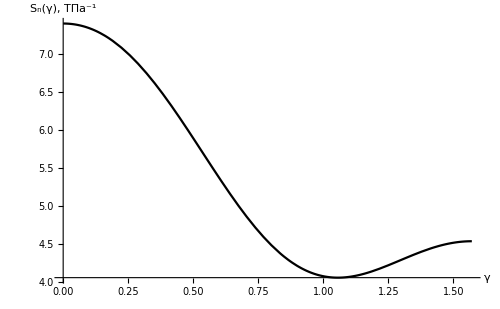

```mathematica
plot5 = Plot[Subscript[S, I, n][Cos[γ],1/(√2)Sin[γ],1/(√2)Sin[γ]], {γ, 0 , π/2},
PlotStyle->{Black, Bold},
AxesLabel->{Style["γ",Large,Black],Style["S_n(γ), (T:041f:0430)^-1",Large,Black]},AxesStyle->Thick, BaseStyle->Directive[FontSize->17,FontWeight->Plain],ImageSize->500]
FileExport[plot5, "I_4"];
```

## Верхние и нижние оценки κ, μ, E, ν

```mathematica
Subscript[κ, +I]= 10^-9*1/3(Subscript[C, I,11]+2 Subscript[C, I, 12]);
```

```mathematica
Subscript[κ, -I]= 10^3/(3*10^12(Subscript[S, I, 11]+ 2 Subscript[S, I, 12]));
```

```mathematica
Subscript[μ, +I]= 10^-9*1/5(Subscript[C, I,11]- Subscript[C, I,12] + 3 Subscript[C, I,44]) ;
```

```mathematica
Subscript[μ, -I]=10^3/(10^12*1/5(4(Subscript[S, I, 11]- Subscript[S, I, 12]) + 3 Subscript[S, I, 44]));
```

```mathematica
Subscript[E, +I]= 1/(1/(9 Subscript[κ, +I])+1/(3 Subscript[μ, +I]));
```

```mathematica
Subscript[E, -I]= 1/(1/(9 Subscript[κ, -I])+1/(3 Subscript[μ, -I]));
```

```mathematica
Subscript[ν, +I]= Subscript[E, -I]/(2 Subscript[μ, -I])-1;
```

```mathematica
Subscript[ν, -I]= Subscript[E, +I]/(2 Subscript[μ, +I])-1;
```

```mathematica
Subscript[κ, +II]= 10^-9*1/9(2 Subscript[C, II,11]+Subscript[C, II, 33]+2(Subscript[C, II, 12]+ 2 Subscript[C, II, 13]));
```

```mathematica
Subscript[κ, -II]= 10^3/(10^12(2 Subscript[S, II, 11]+Subscript[S, II, 33] +2(Subscript[S, II, 12] + 2 Subscript[S, II, 13])));
```

```mathematica
Subscript[μ, +II]= 10^-9*1/30(7 Subscript[C, II,11]-5 Subscript[C, II,12] - 4 Subscript[C, II,13]+ 2 Subscript[C, II, 33]+ 12 Subscript[C, II, 44]) ;
```

```mathematica
Subscript[μ, -II]=10^3/(10^12*2/15(7 Subscript[S, II, 11] + 2 Subscript[S, II, 33]+ 3 Subscript[S, II, 44]-5 Subscript[S, II, 12]-4 Subscript[S, II, 13]));
```

```mathematica
Subscript[E, +II]= 1/(1/(9 Subscript[κ, +II])+1/(3 Subscript[μ, +II]));
```

```mathematica
Subscript[E, -II]= 1/(1/(9 Subscript[κ, -II])+1/(3 Subscript[μ, -II]));
```

```mathematica
Subscript[ν, +II]= Subscript[E, -II]/(2 Subscript[μ, -II])-1;
```

```mathematica
Subscript[ν, -II]= Subscript[E, +II]/(2 Subscript[μ, +II])-1;
```

```mathematica
Grid[N@{{ "","-", "+"}, {"κ_I", Subscript[κ, -I], Subscript[κ, +I]}, {"μ_I", Subscript[μ, -I], Subscript[μ, +I]}, {"E_I", Subscript[E, -I], Subscript[E, +I]},{"ν_I", Subscript[ν, -I], Subscript[ν, +I]}, {"κ_II",Subscript[κ, -II],Subscript[κ, +II] }, {"μ_II", Subscript[μ, -II], Subscript[μ, +II]}, {"E_II", Subscript[E, -II], Subscript[E, +II]}, {"ν_II", Subscript[ν, -II], Subscript[ν, +II]} }, Frame->All,FrameStyle->Bold,Spacings->{1,1},ItemStyle->Directive[FontSize->14]]
```

| - | +
κ_I | 168. | 168.
μ_I | 74.9402 | 88.2
E_I | 195.719 | 225.191
ν_I | 0.276596 | 0.305834
κ_II | 47.8469 | 59.1413
μ_II | 18.9117 | 24.4079
E_II | 50.1303 | 64.3686
ν_II | 0.318602 | 0.325379

## Задача Эшелби

```mathematica
δ = IdentityMatrix[6];
```

```mathematica
Subscript[C, 0]= ({{κ+(4 μ)/3, κ-(2μ)/3, κ-(2μ)/3, 0, 0, 0}, {κ-(2μ)/3, κ+(4 μ)/3, κ-(2μ)/3, 0, 0, 0}, {κ-(2μ)/3, κ-(2μ)/3, κ+(4 μ)/3, 0, 0, 0}, {0, 0, 0, μ, 0, 0}, {0, 0, 0, 0, μ, 0}, {0, 0, 0, 0, 0, μ}});
```

```mathematica
Subscript[δ, sup] = ({{1, 1, 1, 0, 0, 0}, {1, 1, 1, 0, 0, 0}, {1, 1, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}});
```

```mathematica
Subscript[I, 6] = ({{1, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0}, {0, 0, 0, 2, 0, 0}, {0, 0, 0, 0, 2, 0}, {0, 0, 0, 0, 0, 2}});
```

```mathematica
Iikik[A_] := Sum[A[[i,i]],{i,1,3}]+2 Sum[A[[i,i]],{i,4,6}];
Iiikk[A_]:=Sum[A[[i,j]],{i,1,3},{j,1,3}];
```

```mathematica
ν=(3κ-2μ)/(6κ+2μ);
w=3/2*(1-ν)/(4-5ν)((1-5ν)/(1+ν)Subscript[δ, sup]+5 Subscript[I, 6]);
```

```mathematica
ζm[A_]:=Inverse[A-Subscript[C, 0].(δ-w)].(Subscript[C, 0]-A);
```

```mathematica
Subscript[κ, +-I] = (Subscript[κ, +I]+ Subscript[κ, -I])/2 // N
Subscript[μ, +-I] = (Subscript[μ, +I]+ Subscript[μ, -I])/2 // N
Subscript[κ, +-II] = (Subscript[κ, +II]+ Subscript[κ, -II])/2 // N
Subscript[μ, +-II] = (Subscript[μ, +II]+ Subscript[μ, -II])/2 // N
```

168.

81.5701

53.4941

21.6598

```mathematica
Subscript[ζ, minI] =FindMinimum[(Iikik[ζm[10^-9 Subscript[C, I]]])^2+(Iiikk[ζm[10^-9 Subscript[C, I]]])^2,{{κ,Subscript[κ, +-I]},{μ,Subscript[μ, +-I]}},Method->"ConjugateGradient"]⟦2⟧
```

{κ→168.,μ→83.4291}

```mathematica
Subscript[E, minI]= 1/(1/(9 κ)+1/(3 μ))/. Subscript[ζ, minI]
```

214.741

```mathematica
Subscript[ν, minI]=Subscript[E, minI]/(2μ)-1/. Subscript[ζ, minI]
```

0.286964

```mathematica
Subscript[ζ, minII] = FindMinimum[(Iikik[ζm[10^-9 Subscript[C, II]]])^2+(Iiikk[ζm[10^-9 Subscript[C, II]]])^2,{{κ,Subscript[κ, +-II]},{μ,Subscript[μ, +-II]}},Method->"ConjugateGradient"][[2]]
```

{κ→54.9638,μ→22.1267}

```mathematica
Subscript[E, minII]= 1/(1/(9 κ)+1/(3 μ))/. Subscript[ζ, minII]
```

58.5265

```mathematica
Subscript[ν, minII]=Subscript[E, minII]/(2μ)-1/. Subscript[ζ, minII]
```

0.32253

## Расчеты для пористого двухфазного сплава-смеси I-II

```mathematica
VI[V_, V3_]:= V(1-V3)
VII[V_, V3_]:= 1-V3-VI[V,V3]
```

```mathematica
κF[V_, V3_]:= VI[V, V3] Subscript[κ, +I] + VII[V, V3] Subscript[κ, +II]
μF[V_, V3_]:= VI[V, V3] Subscript[μ, +I] + VII[V, V3] Subscript[μ, +II]
EF[V_, V3_]:= 1/(1/(9κF[V, V3])+1/(3μF[V, V3]))
νF[V_, V3_]:=EF[V, V3]/(2μF[V, V3])-1
```

```mathematica
κR[V_, V3_]:= 1/(VI[V, V3]/Subscript[κ, -I]+ VII[V, V3]/Subscript[κ, -II])
μR[V_, V3_]:= 1/(VI[V, V3]/Subscript[μ, -I]+ VII[V, V3]/Subscript[μ, -II])
ER[V_, V3_]:=  1/(1/(9κR[V, V3])+1/(3μR[V, V3]))
νR[V_, V3_]:=ER[V, V3]/(2μR[V, V3])-1
```

### Пористость 0

```mathematica
n=20;h=1/n;t=0.1;
```

```mathematica
ζ0 = ConstantArray[0, {6, 6}];
```

```mathematica
evaluation[j_?IntegerQ]:= Module[
{Vκ, Vμ, VE ,Vν, i, κmid, μmid, ζmin, κesh, μesh, s},
Vκ = {}; Vμ = {}; VE = {}; Vν = {};
For[i = 0, i <= n,i++,
κmid=(κF[i h,j t]+κR[i h,j t])/2;
μmid=(μF[i h,j t]+μR[i h,j t])/2;
ζmin=VI[i h,j t]ζm[10^-9 Subscript[C, I]]+VII[i h,j t]ζm[10^-9 Subscript[C, II]]+j t ζ0;
s=Thread[#⟦1⟧->#⟦2⟧]&/@FindMinimum[(Iikik[ζmin])^2+(Iiikk[ζmin])^2,{{κ,κmid},{μ,μmid}},Method->"PrincipalAxis"][[2]];
{κesh,μesh}={κ,μ}/.s;
AppendTo[Vκ,{i h,κesh}];
AppendTo[Vμ,{i h,μesh}];
AppendTo[VE,{i h,1/(1/(9 κesh)+1/(3μesh))}];
AppendTo[Vν,{i h,VE[[-1,2]]/(2 μesh)-1}];
];

Return[{Vκ, Vμ, VE ,Vν}]
]
```

```mathematica
j0 = 0;
```

```mathematica
{Subscript[V, κ] , Subscript[V, μ], Subscript[V, E], Subscript[V, ν]} = evaluation[j0];
```

```mathematica
MakePlot[data_?ListQ, yLabel_?StringQ, range_?ListQ] := 
ListLinePlot[data, AxesLabel->{Style["V_4",Large,Black],Style[yLabel,18,Black]}, PlotStyle->{{Purple,Thick},{Pink,Thick},{Cyan,Thick}},ImageSize->500,PlotRange->Full, PlotLegends->{"Оценка по Фойгту","Оценка по Эшелби"," Оценка по Рейссу"}, LabelStyle->Directive[Black,18, FontFamily -> "Times"]]
```

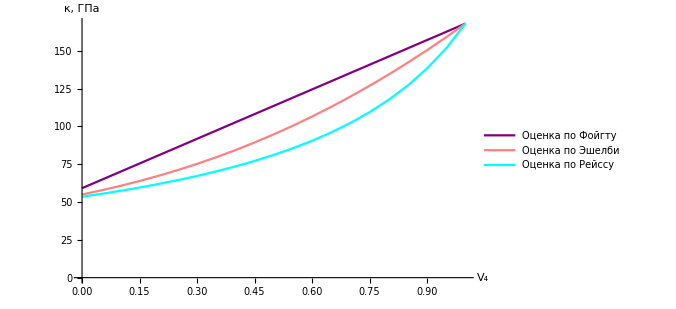

```mathematica
κj0plot = MakePlot[{Table[{i h,κF[i h,j0]},{i,0,n}],Subscript[V, κ],Table[{i h,κR[i h,j0]},{i,0,n}]}, "κ, ГПа", {}]
```

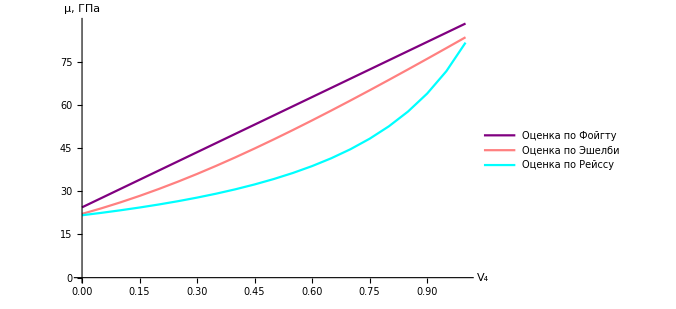

```mathematica
μj0plot = MakePlot[{Table[{i h,μF[i h,j0]},{i,0,n}],Subscript[V, μ],Table[{i h,μR[i h,j0]},{i,0,n}]}, "μ, ГПа", {}]
```

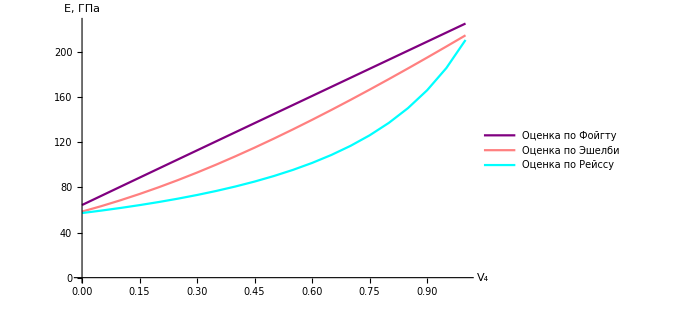

```mathematica
Ej0plot = MakePlot[{Table[{i h,EF[i h,j0]},{i,0,n}],Subscript[V, E],Table[{i h,ER[i h,j0]},{i,0,n}]}, "E, ГПа", {}]
```

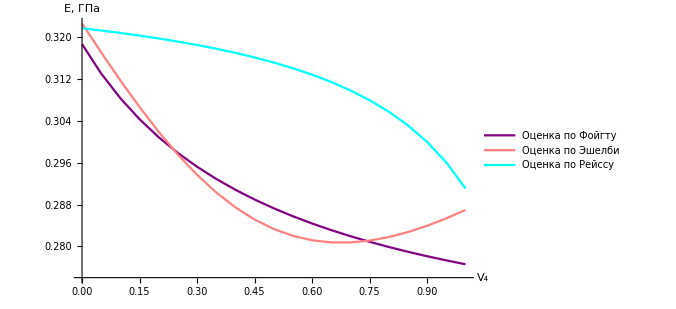

```mathematica
νj0plot = MakePlot[{Table[{i h,νF[i h,j0]},{i,0,n}],Subscript[V, ν],Table[{i h,νR[i h,j0]},{i,0,n}]}, "E, ГПа", {}]
```

```mathematica
j1 = 0.1
```

0.1

```mathematica
{Subscript[V, κ] , Subscript[V, μ], Subscript[V, E], Subscript[V, ν]} = evaluation[j1];
```

Set::shape: Lists {V_κ,V_μ,V_ⅇ,V_ν} and evaluation[0.1] are not the same shape.

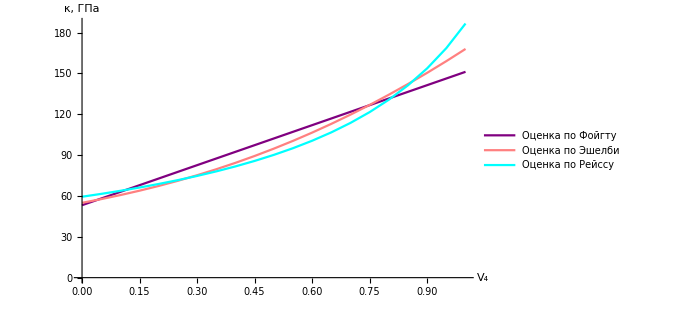

```mathematica
κj1plot = MakePlot[{Table[{i h,κF[i h,j1]},{i,0,n}],Subscript[V, κ],Table[{i h,κR[i h,j1]},{i,0,n}]}, "κ, ГПа", {}]
```

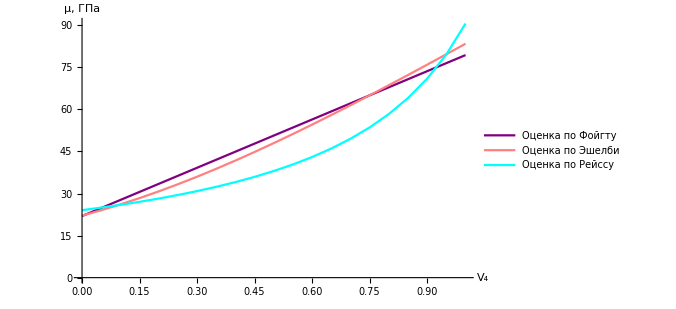

```mathematica
μj1plot = MakePlot[{Table[{i h,μF[i h,j1]},{i,0,n}],Subscript[V, μ],Table[{i h,μR[i h,j1]},{i,0,n}]}, "μ, ГПа", {}]
```

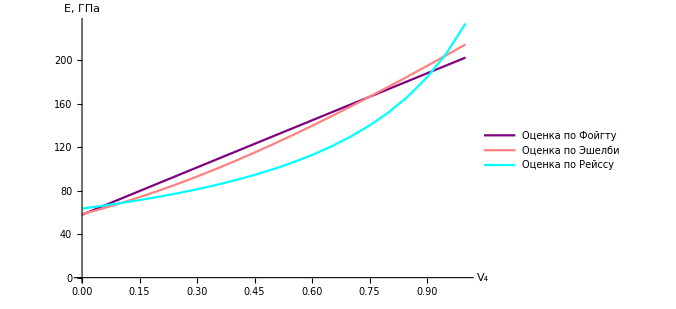

```mathematica
Ej1plot = MakePlot[{Table[{i h,EF[i h,j1]},{i,0,n}],Subscript[V, E],Table[{i h,ER[i h,j1]},{i,0,n}]}, "E, ГПа", {}]
```

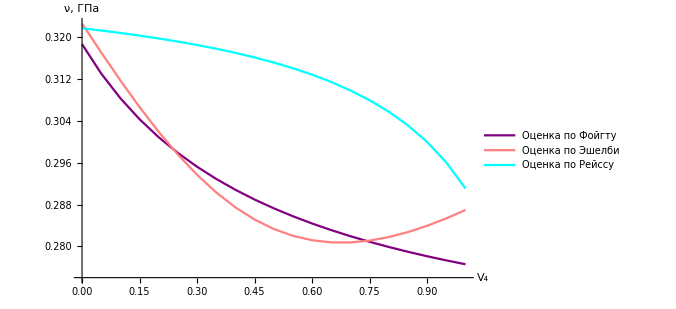

```mathematica
νj1plot = MakePlot[{Table[{i h,νF[i h,j1]},{i,0,n}],Subscript[V, ν],Table[{i h,νR[i h,j1]},{i,0,n}]}, "ν, ГПа", {}]
```

```mathematica
FileExport[κj0plot, "lambdaj0"];
FileExport[μj0plot, "muj0"];
FileExport[Ej0plot, "Ej0"];
FileExport[νj0plot, "nuj0"];
FileExport[κj1plot, "lambdaj1"];
FileExport[μj1plot, "muj1"];
FileExport[Ej1plot, "Ej1"];
FileExport[νj1plot, "nuj1"];
```